```mathematica
ClearAll[data,d,num,f,size]
data="When, in the course of human events, it becomes necessary for one people to dissolve the political bands which have connected them with another, and to assume, among the powers of the earth, the separate and equal station to which the laws of nature and of nature’s God entitle them, a decent respect to the opinions of mankind requires that they should declare the causes which impel them to the separation.";
d=Association@MapThread[Rule,{Join[Alphabet[],{" ",",",".","’"},ToUpperCase@Alphabet[]],Range@56}];
num=d/@Characters@data;
f[x_]:=Times@@MapThread[Power@@{Prime@#1,#2}&,{Range[Length[x]],x}]
num=f@num;
size=Log[2,num]/8//Ceiling
FactorInteger@num;
bytes=IntegerDigits[num,256];
p[x_]:=Partition[PadLeft[x,{Ceiling[Length[x],8]}],8]
file=bytes;
SetDirectory["C:\\Users\\stary\\Desktop"]
Export["a",file,"Byte"]
in=Import["a","Byte"];
in==bytes
```

7267

C:\Users\stary\Desktop

a

True

```mathematica
26*2+3
```

55

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

```mathematica
k
```

k

```mathematica
Monitor[FindFormula[Table[Ceiling@(Log2[Product[Prime[x]^RandomInteger[62],{x,1,y}]]),{y,1,10000,1}]],y]
```

Piecewise[{{-10859.5+312.667 #1+0.0564273 #1^2-0.0000103874 #1^3+7.97373×10^-10 #1^4, 1.≤#1<5001.}, {-178763.+450.293 #1+0.00345456 #1^2, 5001.≤#1<10000.}, {0, True}}]&

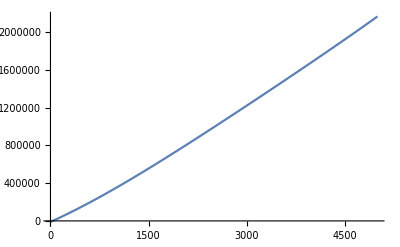

```mathematica
Plot[-10859.467651520165+312.66699247386634 #1+0.05642734042839223 #1^2-0.000010387371866992996 #1^3+7.973730786049285*^-10 #1^4/.#1->x,{x,1,5001}]
```

```mathematica
p@Range@10
```

```mathematica
IntegerDigits[256,256]
```

{1,0}

```mathematica
Ceiling[10,4]
```

12